Raman Sideband Cooling Simulation

## 0. Configuration

Simulation Parameters

```mathematica
nmax = 15;
ΩR = 2.65270037555522*^7;
Ωfree = 2.6965270037555522*^7;
Φ = 135/180 Pi;
ΔRm = 7.3 10^9;
δ1 =  0;
δ2 =+0.01 10^6;  (*repump detuning*)

α = 0.6;

λLat = 532 10^-9;
IntensityLat = 1 /(10^-4);
ω0 = 2 Pi 1.3 10^6;
η = 0.25;

Physical System
```

Physical System

```mathematica
λ = 670.992 10^-9 ;
Γ = 1/(27.102 10^-9);
EFS = 2 Pi 10 10^9 hbar;
ΔR = 10^9;
(*lattice params*)
RCs = 200;(*guess*)
mCs = 6.94 * 1.660539 10^-27 ; (*132.90545*)
```

Physical Constants and auxiliary methods

```mathematica
c = 2.997 10^8;hbar = 1.0545718×10^-34;
ω = c 2 Pi/λ;
ωLat = c * 2 Pi / (λLat);
kb = 1.38066 10^-23;
Dr[n_,nt_]:= √((Min[n,nt]!)/((Min[n,nt]+Abs[nt-n])!))(ⅈ η 1)^Abs[nt-n] LaguerreL[Min[n,nt],Abs[nt-n],(η 1)^2]Exp[-η^2/2];
h = 2 Pi *hbar;(*Sqrt[(3 λ^3 Γ Int)/(2 Pi h c)]*)
```

## 1. Extract Scattering Rates from 3-level Master Equation

```mathematica
Clear[P1list,P2list,P3list];
P1list = {};
P2list = {};
P3list = {};
tab = Table[
Ωn = Ωfree Abs[Dr[n, n - 1]];
If[n == 0, Ωn = 0, dummy = 0];
(*alpha factor to be guessed /measured*)
H = hbar/2({{-2 δ1, Ωn, 0}, {Ωn, 0, ΩR}, {0, ΩR, -2 δ2}});
If[n == 0, α=1, dummy = 0];
Γ1 = α Abs[Dr[n-1, n]]^2 Γ;
Γ2 = (1-α)Abs[Dr[n-1, n - 1]]^2 Γ;
If[n == 0, Γ1 = 0; Γ2 = 0;, dummy = 0];
Γo = Γ - Γ1 - Γ2;

L = ({{Γ1 ρ33[t], 0, -Γ/2 ρ13[t]}, {0, Γ2 ρ33[t], -Γ/2 ρ23[t]}, {-Γ/2 ρ31[t], -Γ/2 ρ32[t], -Γ ρ33[t]}});
ρe[t_] := ({{ρ11[t], ρ12[t], ρ13[t]}, {ρ21[t], ρ22[t], ρ23[t]}, {ρ31[t], ρ32[t], ρ33[t]}});
dρdt =(-ⅈ/hbar(H. ρe[t]- ρe[t]. H)+L);
ρen= Flatten[({{ρ11, ρ12, ρ13}, {ρ21, ρ22, ρ23}, {ρ31, ρ32, ρ33}})];
ρef = Flatten[ρe'[t]];
ρef2 = Flatten[ρe[t]];
dρdtf= Flatten[dρdt];
system = Flatten[Table[Part[ρef,j] == Part[dρdtf,j],{j,1,9,1}]];
init={ρ11[0] == 1, ρ12[0] == 0,ρ13[0] == 0,ρ21[0] == 0,ρ22[0] == 0,ρ23[0] == 0,ρ31[0] == 0,ρ32[0] == 0,ρ33[0] == 0};
sol=NDSolve[Join[system&&init],ρen,{t,0,10^-4}, MaxSteps-> 100000];
fun3=ρ33/.First[sol];
fun1=ρ11/.First[sol];
fun2 = ρ22 /. First[sol];
expsol = Solve[Re[fun3[3 10^-6  ]] == Re[fun3[1 10^-6 ]] Exp[-lp 1 10^-6 ],lp]; 
lar = lp /. expsol;
If[n==0, lam = 0, lam = First[lar] Γ/Γo];

AppendTo[P1list, Re[fun1[2 10^-6 ]] /(Re[fun1[2 10^-6 ]] +Re[fun2[2 10^-6 ]] +Re[fun3[2 10^-6 ]]  )];
AppendTo[P2list, Re[fun2[2 10^-6 ]] /(Re[fun1[2 10^-6 ]] +Re[fun2[2 10^-6 ]] +Re[fun3[2 10^-6 ]]  )];
AppendTo[P3list, Re[fun3[2 10^-6 ]] /(Re[fun1[2 10^-6 ]] +Re[fun2[2 10^-6 ]] +Re[fun3[2 10^-6 ]]  )];

{n,lam}
(*LogPlot[Evaluate[ρe[t]/.sol],{t,0,3*10*10^-5} , PlotRange -> All, PlotRange -> {Automatic, {10^-7,1}}]*)
,{n,0,nmax}]
Γscatt = tab[[All, 2]]
```

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

{{0,0},{1,4.64681×10^6},{2,8.63054×10^6},{3,1.15607×10^7},{4,1.33868×10^7},{5,1.44667×10^7},{6,1.48734×10^7},{7,1.52397×10^7},{8,1.52821×10^7},{9,1.52122×10^7},{10,1.50683×10^7},{11,1.50651×10^7},{12,1.51072×10^7},{13,1.51145×10^7},{14,1.51426×10^7},{15,1.50886×10^7}}

{0,4.64681×10^6,8.63054×10^6,1.15607×10^7,1.33868×10^7,1.44667×10^7,1.48734×10^7,1.52397×10^7,1.52821×10^7,1.52122×10^7,1.50683×10^7,1.50651×10^7,1.51072×10^7,1.51145×10^7,1.51426×10^7,1.50886×10^7}

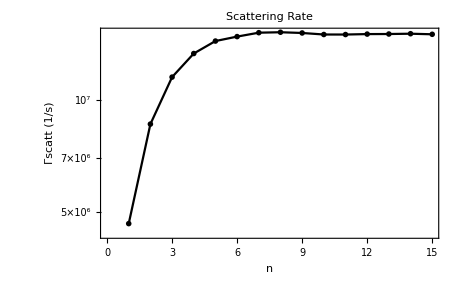

```mathematica
ListLogPlot[tab, FrameLabel-> {"n","Γscatt (1/s)"}, PlotLabel-> "Scattering Rate", Frame-> True, Joined -> True, PlotMarkers->{Automatic, Small}, PlotStyle-> Black, FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

## 2. Calculating Heating and Cooling Rates

```mathematica
Photon recoil
```

```mathematica
Γscatt;
pphoton = h / λ;
Erecoil = pphoton^2/(2mCs); (*has to be corrected actually!!!*)

Λreca= Γscatt * Erecoil;
Λrece= Γscatt * Erecoil;
Λrecarate= Γscatt * Erecoil    2/(3 kb) *10^3;
Λrecerate= Γscatt * Erecoil    2/(3 kb) *10^3
```

{0.,9493.27,17631.9,23618.1,27348.7,29554.9,30385.8,31134.2,31220.7,31078.,30784.,30777.6,30863.6,30878.4,30935.7,30825.5}

```mathematica
Off-resonant scattering: Raman
```

```mathematica
Ephoton = h * c/λ;
ΛscRm =Table[ Γ    (ΩRm1^2* Sum[Abs[Dr[n, m]]^2,{m,0,15}]^2 + ΩRm2^2* Sum[Abs[Dr[n, m]]^2,{m,0,15}]^2)/(4 ΔRm^2)   Erecoil ,{n,0,15}] 2/(3 kb)10^3
```

{4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15931,4.15909,4.15235,4.03409,3.09525,1.11192}

```mathematica
Off-resonant scattering: Repump beam
```

```mathematica
ΛscRp = P1list* Γ ΩR^2/(4 ΔR^2)Erecoil 2/(3 kb)10^3
```

{13.261,10.9924,9.26406,8.03256,7.18976,6.63727,6.28635,6.06664,5.92724,5.838,5.78071,5.74474,5.72455,5.71392,5.71338,5.72083}

```mathematica
Off-Res Raman Couplings: Carrier transitions n-> n
```

```mathematica
Ωcarrier = Table[Ωfree Abs[Dr[n, n]],{n,0,15}];
Λcarrier =0.001 Table[P1list[[n+1]] ΩR^2/Γ Ωcarrier[[n+1]]^2/(4 ω0^2),{n,0,15}]2*Erecoil 2/(3 kb) *10^3  (*cheated*)
```

{199.447,145.308,107.153,80.9005,62.7149,49.8452,40.3768,33.0794,27.2079,22.3457,18.2486,14.767,11.8036,9.28232,7.15433,5.37371}

```mathematica
Off-Res Raman Couplings: Blue transitions
```

```mathematica
Ωblue = Table[Ωfree Abs[Dr[n, n+1]],{n,0,15}]//N;

Λblue= Table[P1list[[n+1]] ΩR^2/Γ Ωblue[[n+1]]^2/(16 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3
```

{31723.3,49357.2,58515.5,63397.7,66425.1,68856.4,71139.5,73300.3,75204.8,76756.,77896.9,78610.7,78916.1,78803.4,78342.7,77559.7}

```mathematica
Off-Res Raman Couplings: Doubly red
```

```mathematica
Ωdoublyred= Table[Ωfree Abs[Dr[n, n-2]],{n,0,15}]//N;

Λdoublyred = -Table[P1list[[n+1]] ΩR^2/Γ Ωdoublyred[[n+1]]^2/(4 ω0^2),{n,0,15}]hbar ω0 2/(3 kb) *10^3 ;
Λdoublyred[[1]] = 0;
Λdoublyred[[2]] = 0;
Λdoublyred
```

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

{0,0,-2770.22,-6908.78,-11855.1,-17480.2,-23793.5,-30792.6,-38414.4,-46574.3,-55177.3,-64132.2,-73365.4,-82771.7,-92324.4,-101962.}

```mathematica
Repumping of state 2
```

```mathematica
α = 0.6;Γheat = Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]]  +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,15}] ;
(*Γ2s = ΩR^2 Γ/(Γ^2+4 δ2^2);*)
ΛRepump = Table[(1-α)/α(Γscatt[[n+1]]+Γheat[[n+1]])Erecoil,{n,0,15}] 2/(3 kb) *10^3
```

{30825.1,34817.8,38178.1,40363.8,41165.,41082.2,40057.8,39138.2,37673.8,36011.1,34195.4,32626.4,31121.2,29529.6,27964.2,26234.2}

```mathematica
Cooling Rate
```

```mathematica
Λcool = -Table[P3list[[n+1]] α Abs[Dr[n-1,n-1]]^2*Γ,{n,0,15}] 2/(3 kb) *10^3 hbar ω0;
Λcool[[1]] = 0;
Λcool
```

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

{0,-54457.,-88908.5,-104246.,-105473.,-98326.7,-87537.3,-75871.6,-64639.4,-54397.4,-45278.9,-37270.9,-30293.2,-24287.4,-19134.1,-14758.3}

```mathematica
Generate table
```

```mathematica
TableOfValues2=MapThread[Prepend,{{{"n = 0","n=1","n=2","n=3","n=4","n=5","n=6","n=7","n=8","n=9","n=10"},Λrecarate, Λrecerate,Λcarrier ,Λblue  ,ΛscRm ,ΛscRp , Λdoublyred,Λcool},{"μK/ms","Λrecarate", "Λrecerate","Λcarrier" ,"Λblue"  ,"ΛscRm" ,"ΛscRp" ,"Λdoublyred","Λcool"}}];
Grid[TableOfValues2[[All,{1,2,3,6,8,10,12}]],ItemStyle->{Automatic,{1->{Bold,14}}},Frame->{All,1->True},Background->{None,{{LightOrange,LightGray}}}]
```

μK/ms | n = 0 | n=1 | n=4 | n=6 | n=8 | n=10
Λrecarate | 0. | 9493.27 | 27348.7 | 30385.8 | 31220.7 | 30784.
Λrecerate | 0. | 9493.27 | 27348.7 | 30385.8 | 31220.7 | 30784.
Λcarrier | 199.447 | 145.308 | 62.7149 | 40.3768 | 27.2079 | 18.2486
Λblue | 31723.3 | 49357.2 | 66425.1 | 71139.5 | 75204.8 | 77896.9
ΛscRm | 4.15931 | 4.15931 | 4.15931 | 4.15931 | 4.15931 | 4.15931
ΛscRp | 13.261 | 10.9924 | 7.18976 | 6.28635 | 5.92724 | 5.78071
Λdoublyred | 0 | 0 | -11855.1 | -23793.5 | -38414.4 | -55177.3
Λcool | 0 | -54457. | -105473. | -87537.3 | -64639.4 | -45278.9

## 3. Matrix Elements (from seperate notebook)

```mathematica
Matrix Elements (from seperate notebook)
```

```mathematica
Matd ={{1.5337604188090186+0. ⅈ,0.11966389269178948+0. ⅈ,0.01156800726156411+0. ⅈ,0.001411048591966118+0. ⅈ,0.00021468875392546886+0. ⅈ,0.00003846590032110959+0. ⅈ,7.807444535791458*^-6+0. ⅈ,1.752707152273474*^-6+0. ⅈ,4.2781137299856986*^-7+0. ⅈ,1.1209643791990949*^-7+0. ⅈ,3.1223296738263093*^-8+0. ⅈ,9.17405856060743*^-9+0. ⅈ,2.8254571391355983*^-9+0. ⅈ,9.063420222659191*^-10+0. ⅈ,2.9795875404897314*^-10+0. ⅈ,9.98857424257307*^-11+0. ⅈ},{0.11966389269178945+0. ⅈ,1.317568647948566+0. ⅈ,0.19728890211322309+0. ⅈ,0.02709648524859807+0. ⅈ,0.004119013838066189+0. ⅈ,0.0007356294336309946+0. ⅈ,0.00014937501756307666+0. ⅈ,0.00003353670260266542+0. ⅈ,8.185543191506932*^-6+0. ⅈ,2.144799442424796*^-6+0. ⅈ,5.974130813190523*^-7+0. ⅈ,1.755324238013795*^-7+0. ⅈ,5.40610523196523*^-8+0. ⅈ,1.7341549846251833*^-8+0. ⅈ,5.701011876762306*^-9+0. ⅈ,1.91116989427912*^-9+0. ⅈ},{0.011568007261564112+0. ⅈ,0.19728890211322322+0. ⅈ,1.1551404700774563+0. ⅈ,0.24927288605279438+0. ⅈ,0.04356765819011158+0. ⅈ,0.007783908963170216+0. ⅈ,0.0015734879499190568+0. ⅈ,0.0003534581650443352+0. ⅈ,0.0000862856998746892+0. ⅈ,0.000022607566015886554+0. ⅈ,6.297096093130969*^-6+0. ⅈ,1.85022663363369*^-6+0. ⅈ,5.698386802326275*^-7+0. ⅈ,1.8279115840044158*^-7+0. ⅈ,6.009235940075373*^-8+0. ⅈ,2.01449696284489*^-8+0. ⅈ},{0.0014110485919661187+0. ⅈ,0.02709648524859808+0. ⅈ,0.2492728860527945+0. ⅈ,1.028984433463344+0. ⅈ,0.28450080953013546+0. ⅈ,0.059701502001262+0. ⅈ,0.012097002433284385+0. ⅈ,0.002701015397591902+0. ⅈ,0.0006597779765406222+0. ⅈ,0.00017291557893999224+0. ⅈ,0.000048159929335859994+0. ⅈ,0.000014150323113285317+0. ⅈ,4.3580951170707355*^-6+0. ⅈ,1.3979765171531368*^-6+0. ⅈ,4.595826661544421*^-7+0. ⅈ,1.5406750506838148*^-7+0. ⅈ},{0.00021468875392546886+0. ⅈ,0.004119013838066189+0. ⅈ,0.04356765819011159+0. ⅈ,0.28450080953013546+0. ⅈ,0.928685162557259+0. ⅈ,0.30823208183895656+0. ⅈ,0.07495341033531347+0. ⅈ,0.01682218579234278+0. ⅈ,0.004076931631546757+0. ⅈ,0.0010691978594604377+0. ⅈ,0.00029791975835811996+0. ⅈ,0.00008752511407614463+0. ⅈ,0.000026955923255357564+0. ⅈ,8.64694464071561*^-6+0. ⅈ,2.842671030081411*^-6+0. ⅈ,9.529573379349921*^-7+0. ⅈ},{0.000038465900321109594+0. ⅈ,0.000735629433630995+0. ⅈ,0.007783908963170215+0. ⅈ,0.059701502001261994+0. ⅈ,0.3082320818389565+0. ⅈ,0.8475752206230598+0. ⅈ,0.3237892281011723+0. ⅈ,0.08911042981100728+0. ⅈ,0.021789140423117807+0. ⅈ,0.005657588272601433+0. ⅈ,0.0015774155924708098+0. ⅈ,0.0004637270344278081+0. ⅈ,0.00014279856828211822+0. ⅈ,0.00004580527740505525+0. ⅈ,0.000015058693809651374+0. ⅈ,5.048180033411273*^-6+0. ⅈ},{7.807444535791461*^-6+0. ⅈ,0.00014937501756307674+0. ⅈ,0.001573487949919057+0. ⅈ,0.012097002433284385+0. ⅈ,0.0749534103353135+0. ⅈ,0.3237892281011725+0. ⅈ,0.7811464707560863+0. ⅈ,0.33338084531452916+0. ⅈ,0.10211370537428019+0. ⅈ,0.026878287380940908+0. ⅈ,0.007402187503414653+0. ⅈ,0.0021771337418679563+0. ⅈ,0.0006710462735876647+0. ⅈ,0.00021521500142190764+0. ⅈ,0.00007074810600626288+0. ⅈ,0.000023717744775128895+0. ⅈ},{1.7527071522734678*^-6+0. ⅈ,0.00003353670260266529+0. ⅈ,0.0003534581650443339+0. ⅈ,0.002701015397591892+0. ⅈ,0.016822185792342723+0. ⅈ,0.089110429811007+0. ⅈ,0.3333808453145265+0. ⅈ,0.7262158098272709+0. ⅈ,0.3385373835587837+0. ⅈ,0.11397570994644733+0. ⅈ,0.03200704994925855+0. ⅈ,0.00927470132716163+0. ⅈ,0.002859180131807137+0. ⅈ,0.000918171364983374+0. ⅈ,0.00030177832369475486+0. ⅈ,0.0001011579210327856+0. ⅈ},{4.278113729983148*^-7+0. ⅈ,8.185543191502053*^-6+0. ⅈ,0.00008628569987463771+0. ⅈ,0.0006597779765402284+0. ⅈ,0.004076931631544328+0. ⅈ,0.021789140423104984+0. ⅈ,0.10211370537421564+0. ⅈ,0.3385373835585461+0. ⅈ,0.6804546454268016+0. ⅈ,0.3403570125912493+0. ⅈ,0.12474014931464827+0. ⅈ,0.03711876564169128+0. ⅈ,0.011243051013147945+0. ⅈ,0.003609227723067272+0. ⅈ,0.0011883209035745655+0. ⅈ,0.00039825800456630965+0. ⅈ},{1.120964379234697*^-7+0. ⅈ,2.1447994424929174*^-6+0. ⅈ,0.00002260756601660457+0. ⅈ,0.000172915578945483+0. ⅈ,0.0010691978594944236+0. ⅈ,0.005657588272781529+0. ⅈ,0.02687828738177181+0. ⅈ,0.11397570995016162+0. ⅈ,0.34035701260873874+0. ⅈ,0.6421081777559666+0. ⅈ,0.33965105849336+0. ⅈ,0.13446087741391782+0. ⅈ,0.04217008287886575+0. ⅈ,0.01326391011603635+0. ⅈ,0.004361997966833031+0. ⅈ,0.0014651675316673044+0. ⅈ},{3.122329675986239*^-8+0. ⅈ,5.97413081732325*^-7+0. ⅈ,6.297096097487105*^-6+0. ⅈ,0.000048159929369172634+0. ⅈ,0.00029791975856427385+0. ⅈ,0.0015774155935634271+0. ⅈ,0.007402187508477785+0. ⅈ,0.03200704997149804+0. ⅈ,0.12474014941796335+0. ⅈ,0.3396510585601643+0. ⅈ,0.6098187799161146+0. ⅈ,0.33702900086964144+0. ⅈ,0.14317654986475595+0. ⅈ,0.04707371964892928+0. ⅈ,0.015126255653191152+0. ⅈ,0.005070508818816466+0. ⅈ},{9.174057921928472*^-9+0. ⅈ,1.7553241158117873*^-7+0. ⅈ,1.8502265048249378*^-6+0. ⅈ,0.000014150322128155827+0. ⅈ,0.00008752510798286732+0. ⅈ,0.0004637270021552676+0. ⅈ,0.0021771335901127928+0. ⅈ,0.009274700679088385+0. ⅈ,0.03711876313733161+0. ⅈ,0.13446086808844626+0. ⅈ,0.33702895733111793+0. ⅈ,0.5824957164328187+0. ⅈ,0.33290562230056575+0. ⅈ,0.15074114864366317+0. ⅈ,0.05119512480852333+0. ⅈ,0.01672187286026799+0. ⅈ},{2.825456475273183*^-9+0. ⅈ,5.406103961760106*^-8+0. ⅈ,5.698385463442789*^-7+0. ⅈ,4.358094093116586*^-6+0. ⅈ,0.000026955916922223944+0. ⅈ,0.00014279853471204797+0. ⅈ,0.0006710461159768814+0. ⅈ,0.002859179467065056+0. ⅈ,0.011243048285669788+0. ⅈ,0.04217007180790023+0. ⅈ,0.14317654919757994+0. ⅈ,0.3329053066608716+0. ⅈ,0.55907209674702+0. ⅈ,0.32716812281399343+0. ⅈ,0.15522945513986833+0. ⅈ,0.05409734531798155+0. ⅈ},{9.064423695639196*^-10+0. ⅈ,1.7343469847463798*^-8+0. ⅈ,1.8281139645402593*^-7+0. ⅈ,1.398131296335814*^-6+0. ⅈ,8.647902011455644*^-6+0. ⅈ,0.00004581034894537425+0. ⅈ,0.00021523882240935977+0. ⅈ,0.000918273052875275+0. ⅈ,0.0036096291691487177+0. ⅈ,0.013265355749100894+0. ⅈ,0.047078733140624704+0. ⅈ,0.15076313287588824+0. ⅈ,0.3271890722929206+0. ⅈ,0.5361782226800967+0. ⅈ,0.3151592705658968+0. ⅈ,0.15628111089847924+0. ⅈ},{2.971474821167179*^-10+0. ⅈ,5.685489356284483*^-9+0. ⅈ,5.992874197975165*^-8+0. ⅈ,4.583313294560272*^-7+0. ⅈ,2.8349311114019883*^-6+0. ⅈ,0.000015017692964316283+0. ⅈ,0.00007055546347695963+0. ⅈ,0.00030095660815248286+0. ⅈ,0.001185089539389658+0. ⅈ,0.004350096666569633+0. ⅈ,0.015084465392968276+0. ⅈ,0.05106265546864549+0. ⅈ,0.15487028036173794+0. ⅈ,0.3127411811338504+0. ⅈ,0.48953250536674353+0. ⅈ,0.3201766640445192+0. ⅈ},{1.0059323284565803*^-10+0. ⅈ,1.9247067044268376*^-9+0. ⅈ,2.0287656389157223*^-8+0. ⅈ,1.551587663614428*^-7+0. ⅈ,9.59707092004951*^-7+0. ⅈ,5.083935576613545*^-6+0. ⅈ,0.000023885771379760085+0. ⅈ,0.00010187430587434378+0. ⅈ,0.0004010695174030868+0. ⅈ,0.0014756523895217467+0. ⅈ,0.005107431178096411+0. ⅈ,0.01681750814919589+0. ⅈ,0.05446740212850906+0. ⅈ,0.16019427500990222+0. ⅈ,0.30446625806509053+0. ⅈ,0.26713032520432095+0. ⅈ}};
```

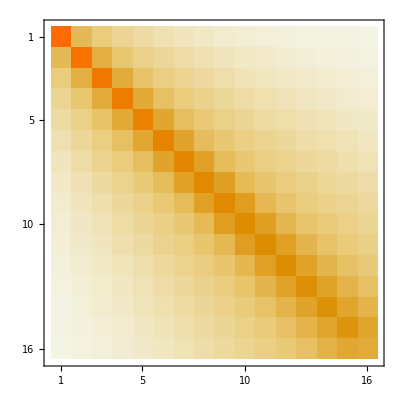

```mathematica
MatrixPlot[Matd,FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

## 4. Dressed State Rate Equation

```mathematica
Γeff[n_]:=Γscatt[[n]]
Γheatpre = Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]]),{n,0,15}] 
Γheat = Table[(Λrecarate[[n+1]]+ Λrecerate[[n+1]]+Λcarrier[[n+1]]+Λblue[[n+1]]  +ΛscRm[[n+1]] +ΛscRp[[n+1]] +Λresc[[n+1]]+ ΛscLat[[n+1]] +  Λdoublyred[[n+1]])α/(3 Erecoil)(2/(3 kb) *10^3)^-1,{n,0,15}]
```

{31940.2,68504.2,91129.7,103818.,109342.,110547.,108168.,104819.,99269.1,92370.1,84315.7,76058.2,67299.6,57807.4,47905.7,37260.6}

{3.12685×10^6,6.70636×10^6,8.92132×10^6,1.01635×10^7,1.07042×10^7,1.08222×10^7,1.05894×10^7,1.02615×10^7,9.71815×10^6,9.04275×10^6,8.25425×10^6,7.44587×10^6,6.58842×10^6,5.65917×10^6,4.68982×10^6,3.6477×10^6}

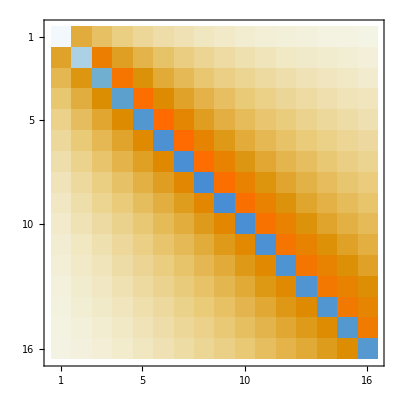

```mathematica
(*Clear[Γeff, Matd, Γheat, α]*)
R = Table[+α(Γeff[n+1]*Matd[[n+1,nt]]+Γheat[[n+1]]*Matd[[n+1,nt+1]]), {n,0,nmax},{nt,0,nmax}] ;
For[i=1,i≤ nmax+1,i++,R[[i,i]] = R[[i,i]] -(Γeff[i]+ Γheat[[i]])];
For[i=1,i≤ nmax+1,i++,R[[i,1]] = α Γheat[[i]]*Matd[[i,1]]];
R[[1,1]] =-(Γeff[1]+ Γheat[[1]]) +  α Γheat[[1]]*Matd[[1,1]];
R //MatrixForm;
MatrixPlot[R, FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}]
```

{P0[0],P1[0],P2[0],P3[0],P4[0],P5[0],P6[0],P7[0],P8[0],P9[0],P10[0],P11[0],P12[0],P13[0],P14[0],P15[0]}=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{P0→InterpolatingFunction[{{0., 0.02}}, <>],P1→InterpolatingFunction[{{0., 0.02}}, <>],P2→InterpolatingFunction[{{0., 0.02}}, <>],P3→InterpolatingFunction[{{0., 0.02}}, <>],P4→InterpolatingFunction[{{0., 0.02}}, <>],P5→InterpolatingFunction[{{0., 0.02}}, <>],P6→InterpolatingFunction[{{0., 0.02}}, <>],P7→InterpolatingFunction[{{0., 0.02}}, <>],P8→InterpolatingFunction[{{0., 0.02}}, <>],P9→InterpolatingFunction[{{0., 0.02}}, <>],P10→InterpolatingFunction[{{0., 0.02}}, <>],P11→InterpolatingFunction[{{0., 0.02}}, <>],P12→InterpolatingFunction[{{0., 0.02}}, <>],P13→InterpolatingFunction[{{0., 0.02}}, <>],P14→InterpolatingFunction[{{0., 0.02}}, <>],P15→InterpolatingFunction[{{0., 0.02}}, <>]}}

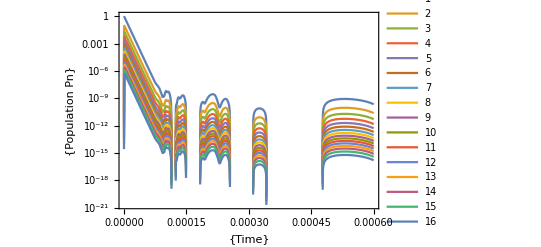

```mathematica
Pm[t_]:= {P0[t],P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]};
Pmen = {P0,P1,P2,P3,P4,P5,P6,P7,P8,P9,P10,P11,P12,P13,P14,P15};
system = Pm'[t] == R.Pm[t] ;
init=Pm[0]=={1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
sol=NDSolve[Flatten[{LogicalExpand[system],LogicalExpand[init]}],Pmen,{t,0,0.02}]
LogPlot[Evaluate[{P0[t], P1[t],P2[t],P3[t],P4[t],P5[t],P6[t],P7[t],P8[t],P9[t],P10[t],P11[t],P12[t],P13[t],P14[t],P15[t]}/.sol],{t,0,0.0006}, PlotRange -> All, Frame-> True, FrameLabel->{{"Time"},{"Population Pn"}},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}, PlotLegends -> Table[n,{n,1,16}]]
```

{4.6851×10^-11,5.02749×10^-12,1.08377×10^-12,3.11763×10^-13,1.08459×10^-13,4.30871×10^-14,1.88787×10^-14,8.8653×10^-15,4.39006×10^-15,2.25594×10^-15,1.18706×10^-15,6.30813×10^-16,3.33499×10^-16,1.7135×10^-16,8.14085×10^-17,3.42476×10^-17}

{0.876336,0.0940378,0.0202715,0.00583143,0.00202869,0.000805932,0.00035312,0.000165823,0.0000821149,0.0000421968,0.0000222036,0.0000117992,6.238×10^-6,3.20505×10^-6,1.52272×10^-6,6.40592×10^-7}

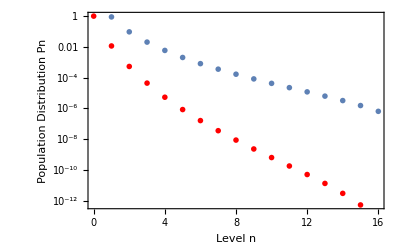

```mathematica
tel = 0.0007;
SteadyState = Table[
func = Pmen[[n+1]]/.First[sol];
steadyvalue = func[tel];
{n, steadyvalue},{n,0,15}];
(*ListLogPlot[SteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"}]*)
SteadySum = Sum[func  = Pmen[[n+1]]/.First[sol];
func[tel], {n,0, nmax}];
NormalizedSteadyStatePre =Table[SteadyState[[n+1]][[2]],{n,0,15}]
NormalizedSteadyState  = Table[NormalizedSteadyStatePre[[n+1]]/SteadySum,{n,0,15}]
p1 =ListLogPlot[NormalizedSteadyState, Joined -> False, PlotMarkers -> {Automatic,Small}, Frame-> True,PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}];
p2 = ListLogPlot[Table[{n,(Normalize[Eigenvectors[R][[16]]][[n+1]])^2},{n,0,nmax}], PlotMarkers -> {Automatic,Small}, PlotStyle -> Red, PlotMarkers -> {Automatic,Small}, Frame-> True, FrameLabel-> {"Level n", "Population Distribution Pn"},FrameStyle -> Black, LabelStyle->Black,BaseStyle->{FontSize->16}];
Show[{p1,p2}, PlotRange -> All]
```

```mathematica
Sum[(Normalize[Eigenvectors[R][[16]]][[n]])^2,{n,1,16}]
```

1.+0. ⅈ

## 5. Calculate Temperature

```mathematica
(*Bose Einstein critic. Temp*)
Nsite = 1 (*1 atom per lkattice site*)
Tc = 0.94 hbar ω0 /kb * Nsite^(1/3)
```

1

0.0000586463

```mathematica
from Simulation
```

```mathematica
GroundStateFraction = NormalizedSteadyState[[0+1]];
Tmin = (1- GroundStateFraction)^(1/3)*Tc *10^6 (*μK*)
```

29.2183

```mathematica
from R Eigenvector
```

```mathematica
GroundStateFraction = (Normalize[Eigenvectors[R][[16]]][[1]])^2;
Tmin = (1- GroundStateFraction)^(1/3)*Tc *10^6 (*μK*)
```

13.4103+0. ⅈ